### Reset Index

```mathematica
(*Get the current Notebook*)
nb=EvaluationNotebook[];
(*Iterate through all cells and reset numbering*)
Module[{cells,count=1},
(*Get all cells in the notebook*)
cells=Cells[nb];
Do[
(*Set new numbering*)
SetOptions[cell,CellLabel->ToString[count]<>". "];
(*Increment the counter for the next cell*)
count++,
(*Loop over all cells*)
{cell,cells} 
]];
```

## GridGraph Operations

```mathematica
DirectedGraph[GridGraph[{5,5}]]
```

-Graphics-

```mathematica
DirectedGraph[GridGraph[{5,5}],Select[EdgeList[GridGraph[{5,5}]],MatchQ[#,UndirectedEdge[{_,_},{_,_}]]&&((#[[1,1]]==#[[2,1]]&&#[[1,2]]<#[[2,2]])||(#[[1,2]]==#[[2,2]]&&#[[1,1]]<#[[2,1]]))&]]
```

-Graphics-

```mathematica
vertices=Flatten[Table[{i,j},{i,5},{j,5}],1];
edges=Join[Table[DirectedEdge[{i,j},{i+1,j}],{i,4},{j,5}],(*South edges*)Table[DirectedEdge[{i,j},{i,j+1}],{i,5},{j,4}]  (*East edges*)];
Graph[vertices,Flatten[edges],DirectedEdges->True,GraphLayout->{"GridEmbedding"}]
```

-Graphics-

```mathematica
Graph[{{1,1},{1,2},{1,3},{1,4},{1,5},{2,1},{2,2},{2,3},{2,4},{2,5},{3,1},{3,2},{3,3},{3,4},{3,5},{4,1},{4,2},{4,3},{4,4},{4,5},{5,1},{5,2},{5,3},{5,4},{5,5}},Flatten[{{{1,1}->{2,1},{1,2}->{2,2},{1,3}->{2,3},{1,4}->{2,4},{1,5}->{2,5}},{{2,1}->{3,1},{2,2}->{3,2},{2,3}->{3,3},{2,4}->{3,4},{2,5}->{3,5}},{{3,1}->{4,1},{3,2}->{4,2},{3,3}->{4,3},{3,4}->{4,4},{3,5}->{4,5}},{{4,1}->{5,1},{4,2}->{5,2},{4,3}->{5,3},{4,4}->{5,4},{4,5}->{5,5}},{{1,1}->{1,2},{1,2}->{1,3},{1,3}->{1,4},{1,4}->{1,5}},{{2,1}->{2,2},{2,2}->{2,3},{2,3}->{2,4},{2,4}->{2,5}},{{3,1}->{3,2},{3,2}->{3,3},{3,3}->{3,4},{3,4}->{3,5}},{{4,1}->{4,2},{4,2}->{4,3},{4,3}->{4,4},{4,4}->{4,5}},{{5,1}->{5,2},{5,2}->{5,3},{5,3}->{5,4},{5,4}->{5,5}}}],DirectedEdges->True,GraphLayout->{"GridEmbedding"}]
```

-Graphics-

```mathematica
Graph[{{1,1},{1,2},{1,3},{1,4},{1,5},{2,1},{2,2},{2,3},{2,4},{2,5},{3,1},{3,2},{3,3},{3,4},{3,5},{4,1},{4,2},{4,3},{4,4},{4,5},{5,1},{5,2},{5,3},{5,4},{5,5}},Flatten[{{{1,1}->{2,1},{1,2}->{2,2},{1,3}->{2,3},{1,4}->{2,4},{1,5}->{2,5}},{{2,1}->{3,1},{2,2}->{3,2},{2,3}->{3,3},{2,4}->{3,4},{2,5}->{3,5}},{{3,1}->{4,1},{3,2}->{4,2},{3,3}->{4,3},{3,4}->{4,4},{3,5}->{4,5}},{{4,1}->{5,1},{4,2}->{5,2},{4,3}->{5,3},{4,4}->{5,4},{4,5}->{5,5}},{{1,1}->{1,2},{1,2}->{1,3},{1,3}->{1,4},{1,4}->{1,5}},{{2,1}->{2,2},{2,2}->{2,3},{2,3}->{2,4},{2,4}->{2,5}},{{3,1}->{3,2},{3,2}->{3,3},{3,3}->{3,4},{3,4}->{3,5}},{{4,1}->{4,2},{4,2}->{4,3},{4,3}->{4,4},{4,4}->{4,5}},{{5,1}->{5,2},{5,2}->{5,3},{5,3}->{5,4},{5,4}->{5,5}}}],DirectedEdges->True,GraphLayout->{"GridEmbedding"}]
```

-Graphics-

```mathematica
vertices=Flatten[Table[{i,j},{i,5},{j,5}],1];
edges=Join[Table[DirectedEdge[{i,j},{i+1,j}],{i,4},{j,5}],Table[DirectedEdge[{i,j},{i,j+1}],{i,5},{j,4}]  ];
Graph[vertices,edges,DirectedEdges->True,GraphLayout->{"GridEmbedding"}]
```

```mathematica
Graph[{{1,1},{1,2},{1,3},{1,4},{1,5},{2,1},{2,2},{2,3},{2,4},{2,5},{3,1},{3,2},{3,3},{3,4},{3,5},{4,1},{4,2},{4,3},{4,4},{4,5},{5,1},{5,2},{5,3},{5,4},{5,5}},Flatten[{{{1,1}->{2,1},{1,2}->{2,2},{1,3}->{2,3},{1,4}->{2,4},{1,5}->{2,5}},{{2,1}->{3,1},{2,2}->{3,2},{2,3}->{3,3},{2,4}->{3,4},{2,5}->{3,5}},{{3,1}->{4,1},{3,2}->{4,2},{3,3}->{4,3},{3,4}->{4,4},{3,5}->{4,5}},{{4,1}->{5,1},{4,2}->{5,2},{4,3}->{5,3},{4,4}->{5,4},{4,5}->{5,5}},{{1,1}->{1,2},{1,2}->{1,3},{1,3}->{1,4},{1,4}->{1,5}},{{2,1}->{2,2},{2,2}->{2,3},{2,3}->{2,4},{2,4}->{2,5}},{{3,1}->{3,2},{3,2}->{3,3},{3,3}->{3,4},{3,4}->{3,5}},{{4,1}->{4,2},{4,2}->{4,3},{4,3}->{4,4},{4,4}->{4,5}},{{5,1}->{5,2},{5,2}->{5,3},{5,3}->{5,4},{5,4}->{5,5}}}],DirectedEdges->True,GraphLayout->{"GridEmbedding"}]
```

-Graphics-

```mathematica
vertices=Flatten[Table[{i,j},{i,5},{j,5}],1];
edges=Join[Table[DirectedEdge[{i,j},{i+1,j}],{i,4},{j,5}],Table[DirectedEdge[{i,j},{i,j+1}],{i,5},{j,4}]];
Graph[vertices,edges,DirectedEdges->True,GraphLayout->{"LayeredEmbedding","Orientation"->Left} ]
```

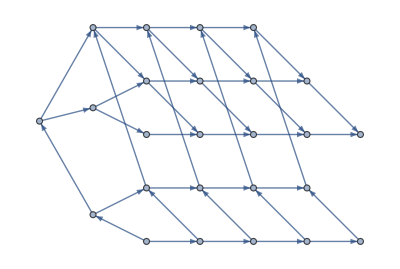

```mathematica
Graph[{{1,1},{1,2},{1,3},{1,4},{1,5},{2,1},{2,2},{2,3},{2,4},{2,5},{3,1},{3,2},{3,3},{3,4},{3,5},{4,1},{4,2},{4,3},{4,4},{4,5},{5,1},{5,2},{5,3},{5,4},{5,5}},Flatten[{{{1,1}->{2,1},{1,2}->{2,2},{1,3}->{2,3},{1,4}->{2,4},{1,5}->{2,5}},{{2,1}->{3,1},{2,2}->{3,2},{2,3}->{3,3},{2,4}->{3,4},{2,5}->{3,5}},{{3,1}->{4,1},{3,2}->{4,2},{3,3}->{4,3},{3,4}->{4,4},{3,5}->{4,5}},{{4,1}->{5,1},{4,2}->{5,2},{4,3}->{5,3},{4,4}->{5,4},{4,5}->{5,5}},{{1,1}->{1,2},{1,2}->{1,3},{1,3}->{1,4},{1,4}->{1,5}},{{2,1}->{2,2},{2,2}->{2,3},{2,3}->{2,4},{2,4}->{2,5}},{{3,1}->{3,2},{3,2}->{3,3},{3,3}->{3,4},{3,4}->{3,5}},{{4,1}->{4,2},{4,2}->{4,3},{4,3}->{4,4},{4,4}->{4,5}},{{5,1}->{5,2},{5,2}->{5,3},{5,3}->{5,4},{5,4}->{5,5}}}],DirectedEdges->True, GraphLayout->{"LayeredEmbedding","Orientation"->Left}]
```

```mathematica
vertices=Flatten[Table[{i,j},{i,5},{j,5}],1];
edges=Join[Table[DirectedEdge[{i,j},{i+1,j}],{i,4},{j,5}],Table[DirectedEdge[{i,j},{i,j+1}],{i,5},{j,4}]  ];
Graph[vertices,edges,DirectedEdges->True,GraphLayout->{"GridEmbedding"}]
```

```mathematica
Graph[{{1,1},{1,2},{1,3},{1,4},{1,5},{2,1},{2,2},{2,3},{2,4},{2,5},{3,1},{3,2},{3,3},{3,4},{3,5},{4,1},{4,2},{4,3},{4,4},{4,5},{5,1},{5,2},{5,3},{5,4},{5,5}},Flatten[{{{1,1}->{2,1},{1,2}->{2,2},{1,3}->{2,3},{1,4}->{2,4},{1,5}->{2,5}},{{2,1}->{3,1},{2,2}->{3,2},{2,3}->{3,3},{2,4}->{3,4},{2,5}->{3,5}},{{3,1}->{4,1},{3,2}->{4,2},{3,3}->{4,3},{3,4}->{4,4},{3,5}->{4,5}},{{4,1}->{5,1},{4,2}->{5,2},{4,3}->{5,3},{4,4}->{5,4},{4,5}->{5,5}},{{1,1}->{1,2},{1,2}->{1,3},{1,3}->{1,4},{1,4}->{1,5}},{{2,1}->{2,2},{2,2}->{2,3},{2,3}->{2,4},{2,4}->{2,5}},{{3,1}->{3,2},{3,2}->{3,3},{3,3}->{3,4},{3,4}->{3,5}},{{4,1}->{4,2},{4,2}->{4,3},{4,3}->{4,4},{4,4}->{4,5}},{{5,1}->{5,2},{5,2}->{5,3},{5,3}->{5,4},{5,4}->{5,5}}}],DirectedEdges->True,GraphLayout->{"GridEmbedding"}]
```

-Graphics-

```mathematica
vertices=Flatten[Table[{i,j},{i,5},{j,5}],1];
edges=Join[Table[DirectedEdge[{i,j},{i+1,j}],{i,4},{j,5}],Table[DirectedEdge[{i,j},{i,j+1}],{i,5},{j,4}]  ];
Graph[vertices,Flatten[edges],DirectedEdges->True,VertexCoordinates->Association[Table[{i,j}->{j,-i},{i,5},{j,5}]//Flatten]]
```

-Graphics-

```mathematica
Graph[{{1,1},{1,2},{1,3},{1,4},{1,5},{2,1},{2,2},{2,3},{2,4},{2,5},{3,1},{3,2},{3,3},{3,4},{3,5},{4,1},{4,2},{4,3},{4,4},{4,5},{5,1},{5,2},{5,3},{5,4},{5,5}},Flatten[{{{1,1}->{2,1},{1,2}->{2,2},{1,3}->{2,3},{1,4}->{2,4},{1,5}->{2,5}},{{2,1}->{3,1},{2,2}->{3,2},{2,3}->{3,3},{2,4}->{3,4},{2,5}->{3,5}},{{3,1}->{4,1},{3,2}->{4,2},{3,3}->{4,3},{3,4}->{4,4},{3,5}->{4,5}},{{4,1}->{5,1},{4,2}->{5,2},{4,3}->{5,3},{4,4}->{5,4},{4,5}->{5,5}},{{1,1}->{1,2},{1,2}->{1,3},{1,3}->{1,4},{1,4}->{1,5}},{{2,1}->{2,2},{2,2}->{2,3},{2,3}->{2,4},{2,4}->{2,5}},{{3,1}->{3,2},{3,2}->{3,3},{3,3}->{3,4},{3,4}->{3,5}},{{4,1}->{4,2},{4,2}->{4,3},{4,3}->{4,4},{4,4}->{4,5}},{{5,1}->{5,2},{5,2}->{5,3},{5,3}->{5,4},{5,4}->{5,5}}}],DirectedEdges->True,VertexCoordinates-><|{1,1}->{1,-1},{1,2}->{2,-1},{1,3}->{3,-1},{1,4}->{4,-1},{1,5}->{5,-1},{2,1}->{1,-2},{2,2}->{2,-2},{2,3}->{3,-2},{2,4}->{4,-2},{2,5}->{5,-2},{3,1}->{1,-3},{3,2}->{2,-3},{3,3}->{3,-3},{3,4}->{4,-3},{3,5}->{5,-3},{4,1}->{1,-4},{4,2}->{2,-4},{4,3}->{3,-4},{4,4}->{4,-4},{4,5}->{5,-4},{5,1}->{1,-5},{5,2}->{2,-5},{5,3}->{3,-5},{5,4}->{4,-5},{5,5}->{5,-5}|>]
```

-Graphics-